# Red neuronal artificial

## Introducción

Una red neuronal artificial (RNA) es un modelo de ajuste basado en el sistema nervioso donde la entrada es un vector x ∈ ℝ^N, y se desea mapear a f(x) ∈ ℝ^M, donde N y M son enteros arbitrariamente grandes. x es el estímulo de entrada que recibe la red, y f(x) es el estímulo de salida. Este modelo está basado en una estructura de capas, donde el estímulo se recibe en la capa de entrada, y el resultado se obtiene en la capa de salida. Cada neurona está interconectada con las demás de la siguiente capa. 
-Graphics-
La fuerza de la conexión entre neuronas está dada por el peso w de la conexión y el bias b. De manera que el resultado de una neurona al procesar la señal es f(∑_i w_ij x_i + b_i), donde f es una función de activación, w_ij es el peso de la conexión de la neurona i con la neurona j, donde i y j están en diferentes capas, y b_i es el bias de la neurona i. Una manera de realizar el conteo de todas las capas que existen en la red neuronal es agregando un tercer índice k, que indique entre qué capas está,  f(∑_i w_ij^k x_i^k + b_i^k).
Un tipo muy usado de neuronas artficiciales es la neurona sigmoide, donde la señal de salida de una neurona en función de su entrada se calcula a través de la función sigmoide.
-Graphics-
La función sigmoide tiene la particularidad de que devuelve siempre un valor entre 0 y 1.

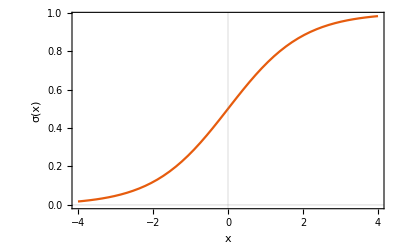

```mathematica
Plot[LogisticSigmoid[x],{x,-4,4}, FrameLabel->{"x","σ(x)"},PlotTheme->"Scientific"]
```

La activación de la neurona está dada por
σ(z) = 1/(1+exp(-∑_j w_ji x_j-b)). 

Por la estructura matemática de este modelo conviene representar todo en forma matricial, de manera que la notación se reduce a
σ(z) = σ(w·x + b).

La propagación hacia delante (feedforward) consiste entonces en aplicar sucesivamente esta función,
x^2 = σ(w^1·x^1+b^1),
x^3 = σ(w^2·x^2+b^2),
⋮
x^N = σ(w^(N-1)·x^(N-1)+b^(N-1)).

La red neuronal trabaja propagando hacia delante la señal inicial mediante la función de activación hasta que se llega a la capa de salida. Si se inicia con una matriz de pesos y bias aleatorios la red neuronal inicialmente no producirá los resultados deseados. La manera en la que podemos determinar qué tan lejos estamos de los resultados es mediante una función de costo
C(w, b) = 1/(2n)∑_x (|y(x)-a|)^2, 

donde w y b son los pesos y los biases.
Con esto se puede conocer cuánto se deben cambiar w y b para que el costo sea menor, es decir, estar más cerca del resultado correcto.
w_k→ w'_k= w_k- η (∂C)/(∂ w_k),
b_l→ b'_l= b_l- η (∂C)/(∂ b_l).

Al aplicar sucesivamente este procedimiento se espera llegar a un resultado cada vez más cercano al correcto. El algoritmo para calcular las derivadas parciales (∂C)/(∂ w_k) y  (∂C)/(∂ b_l) secomoce como el algoritmo de retropropagación. Este consiste en:

Entrada: Establecer la activación a^1 correspondiente para la capa de entrada.

Feedforward: Para cada l = 2,3,…,L se calcula z^l = w^l a^(l-1)+b^l y a^l = σ(z^l).

Error de salida δ^L: Se calcula el vector δ^L = ∇_a C ⊙ σ'(z^L).

Retropropagar el error: Para cada l=L-1, L-2,…,2 calcular δ^l = ((w^(l+1))^T δ^(l+1))⊙σ'(z^l).

Resultado: La derivada parcial de la función de costo es (∂C)/(∂ (w^l)_jk) = a_k^(l-1)δ_j^l y (∂C)/(∂ b_j^l) = δ_j^l.

## Implementación

Esta implementación se basa en la que se ofrece en el libro: http://neuralnetworksanddeeplearning.com.

```mathematica
(* Definición de funciones. *)
Sigmoid[x_]:=LogisticSigmoid[x];
SigmoidPrime[x_] = N[D[LogisticSigmoid[xt],xt] /. xt -> x];

(* El vector de entrada debe ser "vertical". *)
FormatA[array_] := Transpose[{array}];

σ[x_,i_] := LogisticSigmoid[weights[[i]].x + biases[[i]]];

FeedForward[a_] := Fold[σ, a,Range[layers-1]];

Initialize[asizes_, costfunc_:"Quadratic"] :=(
layers = Length[asizes];
sizes = asizes;
bshape = Transpose[{sizes[[2;;]],Table[1,{Length[sizes]-1}]}];
wshape = Transpose[{sizes[[2;;]],sizes[[;;-2]]}];
biases =  Table[RandomVariate[NormalDistribution[],i],{i,bshape}];
weights =Table[RandomVariate[NormalDistribution[],i],{i,wshape}];
emptyNablaB= Table[ConstantArray[0.0,i],{i,bshape}];
emptyNablaW= Table[ConstantArray[0.0,i],{i,wshape}];

(* Definición de funciones relacionadas con el costo. *)
If[costfunc == "Quadratic",
(* Costo cuadrático. *)
Cost[y_,a_]:= 0.5(y-a)^2;
CostPrime[y_,a_]=N[D[Cost[yt,at],at] /. {yt->y,at->a}];
EvalCost[ex_]:=Norm[Cost[ex[[2]],FeedForward[ex[[1]]]]];
CalcDelta[y_,a_,z_]:=  CostPrime[y,a] * SigmoidPrime[z];
,

(* Entropía cruzada. *)
Cost[y_,a_]:= -y Log[a]-(1-y) Log[1-a];
EvalCost[ex_]:=Total[Cost[ex[[2]],FeedForward[ex[[1]]]],2];
CalcDelta[y_,a_,z_]:=  a-y;
];
);

Backprop[x_,y_]:=Module[{nablaB, nablaW, activation,activations,z,zs,delta},
nablaB= emptyNablaB;
nablaW= emptyNablaW;
activation =x;
activations = {x};
zs = {};

(* Calcula todos los feedforwards. *)
Do[
z = weights[[i]].activation + biases[[i]];
activation =LogisticSigmoid[z];
AppendTo[zs,z];
AppendTo[activations, activation];
,{i,1,layers-1}
];

(* Calcula los errores de salida y retropropaga. *)
delta = CalcDelta[y,activations[[-1]] ,zs[[-1]]];
nablaB[[-1]] = delta;
nablaW[[-1]] = delta.Transpose[activations[[-2]]];

Do[
delta = Transpose[weights[[-l+1]]].delta * SigmoidPrime[zs[[-l]]];
nablaB[[-l]] = delta;
nablaW[[-l]] = delta.Transpose[activations[[-l-1]]];
,{l,2,layers-1}
];
Return[{nablaB,nablaW}];
];

(* Realiza el entrenamiento de la red neuronal. *)
TrainNetwork[trainingdata_, epochs_,minibatchsize_,eta_] :=Module[{n, minibatches,dbiases,dweights},
costs = {};

Monitor[
Do[
AppendTo[costs,Mean[Table[EvalCost[ex],{ex,trainingdata}]]];
minibatches = Partition[RandomSample[trainingdata],minibatchsize];
Do[
(* Update mini batch: Calcula los valores de las derivadas parciales del costo y con esto actualiza los pesos y biases. *)
{biases, weights} -=   N[eta/Length[mb]]*Total[Table[Backprop[FormatA[i[[1]]],i[[2]]],{i,mb}]];
,{mb,minibatches}
];
,{j, 1,epochs}
],
Row[{ProgressIndicator[j,{1,epochs}],j, " "}," "]
]
];

(* Igual que TrainNetwork pero guarda los valores de los cambios en biases y weights cada "every" iteraciones. Tiene un mayor consumo de memoria. *)
TrainNetworkAndMonitor[trainingdata_, epochs_,minibatchsize_,eta_, every_:1] :=Module[{n, minibatches,dbiases,dweights,ev},
costs = {};
deltaws = {};
deltabs = {};
ev = 0;

Monitor[
Do[
ClearSystemCache[];
AppendTo[costs,Mean[Table[EvalCost[ex],{ex,trainingdata}]]];
minibatches = Partition[RandomSample[trainingdata],minibatchsize];
Do[
(* Update mini batch: Calcula los valores de las derivadas parciales del costo y con esto actualiza los pesos y biases. *)
{dbiases,dweights} =  N[eta/Length[mb]]*Total[Table[Backprop[FormatA[i[[1]]],i[[2]]],{i,mb}]];
{biases, weights} -=  {dbiases,dweights};
If[Mod[ev,every] == 0,
AppendTo[deltaws,dweights];
AppendTo[deltabs,dbiases];
];
ev++;
,{mb,minibatches}
];
,{j, 1,epochs}
],
Row[{ProgressIndicator[j,{1,epochs}],j, " "}," "]
]
];

(* Utilidades *)
ViewTensor[t_]:= Print[Table[MatrixForm[i],{i,t}]];

ShowCostFunc[] := Print[ListPlot[costs,PlotRange->Full, FrameLabel->{"Iteración","Costo"},PlotTheme->"Scientific", PlotLabel->"Valores de la función de costo"]];

ShowInfo[] :=(
Print["Información del resultado:"];
(* Gráfica del costo. *)
ShowCostFunc[];

(* Mapa del cambio del peso entre las neuronas. *)
max=Table[Max[Table[Max[deltaws[[i]][[1]]],{i,1,Length[deltaws]}]],{Length[deltaws[[1]]]}];
Print[
Manipulate[
cmax = max[[c]];
ArrayPlot[deltaws[[i]][[c]], PlotRange->p, FrameLabel->{"Neurona i", "Neurona j"}, FrameTicks->Automatic,PlotLegends->Automatic, PlotLabel->"Cambio de los pesos entre neuronas"]
,
{{c,1,"Capa"}, 1,Length[deltaws[[1]]],1},
{{i,1,"Iteracion"},1,Length[deltaws],1},
{{p,Automatic, "Rango del color"},{Automatic->"Automático", cmax->"Escalado al máximo"}},
TrackedSymbols:>{c,i,p}
]
];

(* Mapa del cambio total *)
totalchangemap =Table[Sum[deltaws[[i]][[c]],{i,1,Length[deltaws]}], {c,1,Length[deltaws[[1]]]}];
Print[
Manipulate[
ArrayPlot[totalchangemap[[c]],PlotLegends->Automatic,FrameLabel->{"Neurona i", "Neurona j"}, FrameTicks->Automatic, PlotLabel->"Cambio total"]
,{{c,1,"Capa"}, 1,Length[deltaws[[1]]],1},
TrackedSymbols:>{c},
SynchronousUpdating->False
]
];
);
ShowResults[feed_] := Module[{},
Do[
Print[ToString[i] <> " → " <> ToString[FeedForward[i],StandardForm]];
,{i,feed}]
];
```

Aplicación: Compuertas lógicas

La aplicación más trivial de una red neuronal artificial es que aprenda a calcular las salidas de una compuerta lógica. Primero se calculará la compuerta AND.

Datos de entrenamiento.

{0,0} | {0}
{0,1} | {0}
{1,0} | {0}
{1,1} | {1}

Los resultados de la red sin entrenar son:

{0, 0} → {{0.687519}}

{0, 1} → {{0.391784}}

{1, 0} → {{0.459526}}

{1, 1} → {{0.19931}}

Los resultados de la red entrenada son:

{0, 0} → {{0.000124191}}

{0, 1} → {{0.044854}}

{1, 0} → {{0.044854}}

{1, 1} → {{0.946681}}

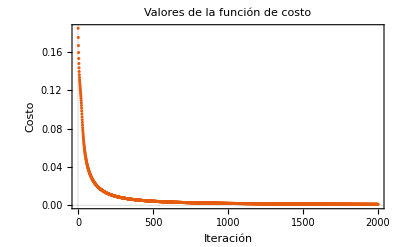

```mathematica
td = {{{0,0},{0}},{{0,1},{0}},{{1,0},{0}},{{1,1},{1}}}; (* Datos de entrenamiento. *)
Print["Datos de entrenamiento."];
Grid[td, Frame-> All]
feed = Table[i[[1]],{i,td}];
Initialize[{2,1}]; (* Se inicia una red neuronal de 2 neuronas en la capa de entrada y 1 en la de salida. *)
Print["Los resultados de la red sin entrenar son:"];
ShowResults[feed];
TrainNetwork[td,2000,4,3]; (* Se entrena la red con 2000 iteraciones, sets de 4 elementos y η = 3. *)
Print["Los resultados de la red entrenada son:"];
ShowResults[feed];
ShowCostFunc[]
```

Al grafica la salida de la red neuronal respecto a los valores de entrada llamando al primer valor de entrada x y al segundo y, se obtiene la gráfica siguiente.

```mathematica
ExpectedAND[x_,y_] := Piecewise[{{0,(x<0.5) || (y<0.5)}, {1,(x>0.5) && (y>0.5)}}];
Plot3D[{FeedForward[{x,y}][[1]][[1]],ExpectedAND[x,y]},{x,0,1},{y,0,1},Filling->Bottom, Mesh->None,PlotStyle->Directive[Opacity[0.8]], PlotLegends->{"Red neuronal","Objetivo"},AxesLabel->{"x","y"}]
```

-Graphics3D-

La compuerta XOR es un poco más complicada, y necesita una red con una capa oculta. Si no se agrega esta capa oculta la red converge a dar 0.5 como resultado en todas las entradas.

Datos de entrenamiento.

{0,0} | {0}
{0,1} | {1}
{1,0} | {1}
{1,1} | {0}

Los resultados de la red sin entrenar son:

{0, 0} → {{0.345931}}

{0, 1} → {{0.363893}}

{1, 0} → {{0.338696}}

{1, 1} → {{0.308724}}

Los resultados de la red entrenada son:

{0, 0} → {{0.036701}}

{0, 1} → {{0.967671}}

{1, 0} → {{0.967633}}

{1, 1} → {{0.0337957}}

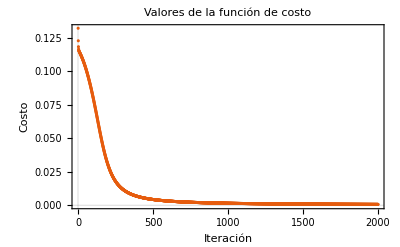

-Graphics3D-

```mathematica
td = {{{0,0},{0}},{{0,1},{1}},{{1,0},{1}},{{1,1},{0}}}; (* Datos de entrenamiento. *)
Print["Datos de entrenamiento."];
Grid[td, Frame-> All]
feed = Table[i[[1]],{i,td}];
Initialize[{2,2,1},"Quadratic"]; (* Se inicia una red neuronal de 2 neuronas en la capa de entrada, 2 en la capa oculta y 1 en la de salida. *)
Print["Los resultados de la red sin entrenar son:"];
ShowResults[feed];
TrainNetwork[td,2000,4,3]; (* Se entrena la red con 2000 iteraciones, sets de 4 elementos y η = 3. *)
Print["Los resultados de la red entrenada son:"];
ShowResults[feed];
ShowCostFunc[]
Plot3D[FeedForward[{x,y}][[1]][[1]],{x,0,1},{y,0,1}, PlotLabel->"Resultado de la red neuronal",AxesLabel->{"x","y"}]
```

Aplicación: Ajuste de una función

Se puede ajustar una función simple utilizando una RNA de una capa de entrada de tamaño 1, una capa intermedia de tamaño indeterminado y otra capa de salida de tamaño 1. El tipo de función y el rango que se puede ajustar es limitado, pero es ilustrativo. A continuación se muestra un ajuste de una función sin(2πx) en un rango [0, 0.5].

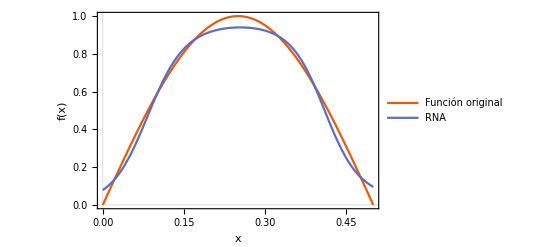

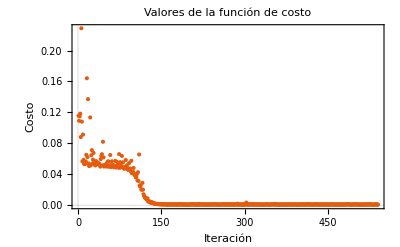

```mathematica
f[x_] := Sin[2 π x];
td = Table[{{x},{f[x]}},{x,0,0.5,0.01}];
Initialize[{1,30,1}]; 
TrainNetwork[td,540,2,5];
Plot[{f[x],FeedForward[{x}][[1]][[1]]},{x,0,0.5},PlotRange->Full, PlotTheme->"Scientific",FrameLabel->{"x", "f(x)"}, PlotLegends->{"Función original","RNA"}]
ShowCostFunc[]
```

Cabe preguntarse cuál ha de ser el tamaño de la capa intermedia para obtener un ajuste óptimo. Al graficar el costo final respecto al tamaño de la capa intermedia se puede observar que alrededor de 15 es seguro obtener un buen resultado.

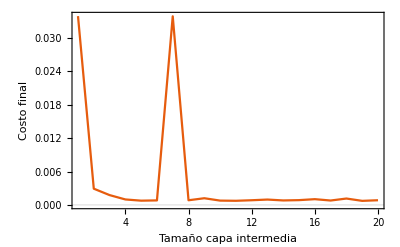

```mathematica
TrainFunc[middlelayer_, iter_]:= Module[{},
Initialize[{1,middlelayer,1}]; 
TrainNetwork[td,iter,2,5];
Return[costs[[-1]]];
];

f[x_] := Sin[2 π x];
td = Table[{{x},{f[x]}},{x,0,0.5,0.01}];
rescost=Table[TrainFunc[i,500],{i,1,20}];
ListLinePlot[rescost,PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"Tamaño capa intermedia", "Costo final"}]
```

Aplicación: Determinar el idioma de un texto

El objetivo de esta aplicación es determinar el idioma de una cadena de texto. Cada idioma posee una distribución característica de la frecuencia de aparición de cada uno de sus caracteres. Aprovechando este tipo de distribución se puede entrenar una red neuronal.

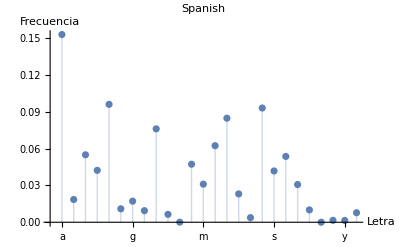

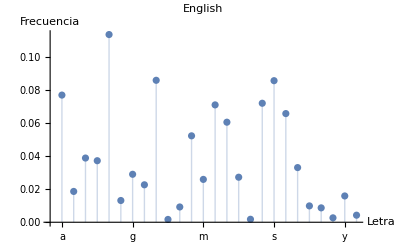

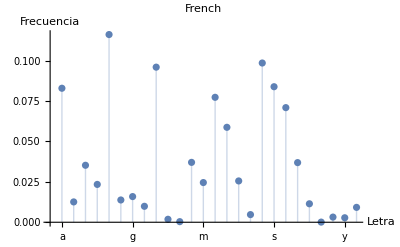

```mathematica
GenLangDist[lang_]:=Module[{joineddict,diclen,dictcounts,dictfrec},joineddict=StringJoin[DictionaryLookup[{lang,All}]];
diclen=StringLength[joineddict];
dictcounts=CharacterCounts[joineddict];
dictfrec=Table[dictcounts[[i]]/diclen,{i,Alphabet[]}];
ListPlot[dictfrec,Ticks->{Thread[{Table[i,{i,Length[CharacterRange["a","z"]]}],CharacterRange["a","z"]}],Automatic,{-1,1}},Filling->Axis,AxesLabel->{"Letra","Frecuencia"},BaseStyle->{FontSize->13},PlotLabel->lang]
];
GenLangDist["Spanish"]
GenLangDist["English"]
GenLangDist["French"]
```

El entrenamiento no se realizará sobre el diccionario debido a que el objetivo es clasificar un texto, y en los textos la distribución de frecuencia de caracteres es modificada por las palabras que se suelen repetir más comúnmente. Los datos de entrenamiento se generarán a partir de muestras de textos. El muestreo se realiza seleccionando partes aleatorias del texto y contando la frecuencia de aparición de cada caracter. Esto genera una lista de 26 elementos, donde cada una corresponde a la frecuencia de aparición de cada letra en orden alfabético. Los textos de entrenamiento disponibles están en los idiomas Español, Ingles, Francés y Alemán.

```mathematica
categoricalConvTable = {};
GetTrainingData[] := Module[{path, files, samplesize, samples, trainingdata,text,langname, del, len, samplepos, textsample,counts,dist,languages,basearray},
path = NotebookDirectory[] <> "TrainingData/";
SetDirectory[path];
files = FileNames[];
samplesize= 5000;
samples = 50;
trainingdata = {};

Do[
langname = FileBaseName[f];
text =Import[f];
text = ToLowerCase[text];
text = StringReplace[text,{"á"-> "a", "é" -> "e","í"-> "i", "ó" -> "o", "ú" -> "u", "ñ" -> "n", "ü" -> "u"}];
del = Complement[Keys[CharacterCounts[text]],Alphabet[]];
text = StringReplace[text,del-> ""];
len = StringLength[text];

(* Genera muestras y toma la distribución *)
Do[
samplepos = RandomInteger[{1,len-samplesize}];
textsample = StringTake[text,{samplepos,samplepos+samplesize}];
counts = CharacterCounts[textsample];
dist = Table[counts[[i]]/samplesize,{i, Alphabet[]}];
dist = {dist,langname};
dist = ReplaceAll[dist,Missing[_,_]->0];
AppendTo[trainingdata,dist];
,{samples}
];
,{f,files}
];

languages = DeleteDuplicates[trainingdata[[All,2]]];
basearray = ConstantArray[0,Length[languages]];
categoricalConvTable = Table[{languages[[i]], ReplacePart[basearray,i-> 1]},{i,1,Length[languages]}];
Return[trainingdata];
];

CategoricalToNumeric[td_] := Module[{data},
data = td;
Do[
data = ReplaceAll[data,categoricalConvTable[[i]][[1]] -> categoricalConvTable[[i]][[2]]];
,{i,1,Length[categoricalConvTable]}
];
Return[data];
];

NumericToCategorical[list_] := Module[{data,found},
data = list;
found = 0;
Do[
found += Count[{data},categoricalConvTable[[i]][[2]]];
,{i,1,Length[categoricalConvTable]}
];

If[found ≠ 0,
Do[
data = Replace[data,categoricalConvTable[[i]][[2]] -> categoricalConvTable[[i]][[1]]];
,{i,1,Length[categoricalConvTable]}
];
Return[data];,
Return["Clasificación erronea"];
]
];

GetDistFromText[text_]:=Module[{t,del,counts,dist,samplesize},
t = text;
t = ToLowerCase[t];
t=  StringReplace[t,{"á"-> "a", "é" -> "e","í"-> "i", "ó" -> "o", "ú" -> "u", "ñ" -> "n", "ü" -> "u"}];
del = Complement[Keys[CharacterCounts[t]],Alphabet[]];
t = StringReplace[t,del-> ""];
counts = CharacterCounts[t];
samplesize = StringLength[t];
dist = Table[counts[[i]]/samplesize,{i, Alphabet[]}];
dist = ReplaceAll[dist,Missing[_,_]->0];
Return[dist];
];

GetRandomTestData[] :=Module[{path, files, samplesize, samples, trainingdata, f,langname,text,del,len,samplepos,textsample,counts,dist},
path = NotebookDirectory[] <> "TrainingData/";
SetDirectory[path];
files = FileNames[];
samplesize= 5000;
samples = 50;
trainingdata = {};
f = RandomSample[files,1][[1]];

langname = FileBaseName[f];
text =Import[f];
text = ToLowerCase[text];
text = StringReplace[text,{"á"-> "a", "é" -> "e","í"-> "i", "ó" -> "o", "ú" -> "u", "ñ" -> "n", "ü" -> "u"}];
del = Complement[Keys[CharacterCounts[text]],Alphabet[]];
text = StringReplace[text,del-> ""];
len = StringLength[text];

samplepos = RandomInteger[{1,len-samplesize}];
textsample = StringTake[text,{samplepos,samplepos+samplesize}];
counts = CharacterCounts[textsample];
dist = Table[counts[[i]]/samplesize,{i, Alphabet[]}];
dist = {dist,CategoricalToNumeric[langname]};
dist = ReplaceAll[dist,Missing[_,_]->0];
Return[dist];
];

ScoreResults[td_,trials_:100]:= Module[{data,score},
score = 0;
Do[
data = GetRandomTestData[];
If[data[[2]] == Round[Flatten[FeedForward[data[[1]]]]], score++];
,{trials}
];
Print["Pruebas superadas: " <> ToString[score] <> " de " <> ToString[trials] <> "."];
];
ClassifyText[text_] := Module[{dist},
dist = GetDistFromText[text];
Print["Resultado de la clasificación: " <> NumericToCategorical[Round[Flatten[FeedForward[dist]]]]];
];

td =CategoricalToNumeric[GetTrainingData[]];
Initialize[{26,26,4},"CrossEntropy"]; 
TrainNetworkAndMonitor[td,200,10,3];
Print["Test 1."];
ScoreResults[td];
Print["Test 2."];
ClassifyText["En el principio creó Dios los cielos y la tierra. Y la tierra estaba desordenada y vacía, y las tinieblas estaban sobre la faz del abismo, y el Espíritu de Dios se movía sobre la faz de las aguas. Y dijo Dios: Sea la luz; y fue la luz. Y vio Dios que la luz era buena; y separó Dios la luz de las tinieblas. Y llamó Dios a la luz Día, y a las tinieblas llamó Noche. Y fue la tarde y la mañana un día."]

ClassifyText["In the beginning God created the heaven and the earth. And the earth was waste and void; and darkness was upon the face of the deep: and the spirit of God moved upon the face of the waters. And God said, Let there be light: and there was light. And God saw the light, that it was good: and God divided the light from the darkness. And God called the light Day, and the darkness he called Night. And there was evening and there was morning, one day."]
ShowInfo[]
```

Aplicación: Clasificar dígitos

Utilizando una RNA se puede obtener un buen nivel de precisión a la hora de clasificar dígitos. Para esto se usará la base de datos MNIST que consiste de 60000 ejemplos de dígitos en imágenes de bloques de 28x28 pixeles.  

-Graphics-

Cada imagen se transforma en un vector de entrada de 784 neuronas, y el resultado es un vector de 10 neuronas donde la activación en la neurona N representa que el dígito N fue encontrado. Por ejemplo, si se encuentra un 5 el resultado en la capa de salida será (0, 0, 0, 0, 1, 0, 0, 0, 0). Para fines prácticos se reducirá el tiempo de cómputo tratando de clasificar sólo dos dígitos: 0 y 1.

```mathematica
DigitToOutput[index_]:= Module[{out},
out = ConstantArray[0,{2}];
out[[index+1]] = 1;
Return[out];
];

OutputToDigit[out_]:= Module[{pos},
pos = Position[out,1];
If[Length[pos] == 1,
Return[pos[[1]][[1]]-1];,
Return["Clasificación erronea"];
]
];

ScoreResults[td_]:= Module[{data,score},
score = 0;
Do[
If[d[[2]] == Round[Flatten[FeedForward[d[[1]]],1]], score++];
,{d,td}
];
Print["Pruebas superadas: " <> ToString[score] <> " de " <> ToString[Length[td]] <> "."];
];

(* Conjunto de entrenamiento. Para disminuir el tiempo de evaluación la red sólo se entrenará para reconocer unos y ceros. *)
(* 0: 1-5923, 1: 5924-12665 *)
td=ExampleData[{"MachineLearning","MNIST"},"TrainingData"][[1;;12665]];
td = Table[{Flatten[ImageData[td[[i]][[1]]]],DigitToOutput[td[[i]][[2]]]},{i,1,Length[td]}];
td[[All,1]] = 1-td[[All,1]];

(* Conjunto de prueba. *)
(* 0: 1-980, 1: 981-2115 *)
testdata = ExampleData[{"MachineLearning","MNIST"},"TestData"][[1;;2115]];
testdata = Table[{Flatten[ImageData[testdata[[i]][[1]]]],DigitToOutput[testdata[[i]][[2]]]},{i,1,Length[testdata]}];
testdata[[All,1]] = 1-testdata[[All,1]];

(* Inicio del entrenamiento y pruebas. *)
Initialize[{784,30,2}]; 
TrainNetworkAndMonitor[td,10,2,10,500];
ScoreResults[testdata]
ShowInfo[]
```